# Retrospective evaluation of school-related measures on pre-vaccination dynamics of SARS-CoV-2

## Canfora B., Escosio R. A., Boldea O., van Dorp C. H., Nunes A., and Rozhnova G.

## Preliminaries

## Memory and global parameters

```mathematica
ResourceFunction["DarkMode"][False]

(* Clear *)
$HistoryLength=0;
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
Off[General::munfl]
memory:=Row[{"Memory Used:",MemoryInUse[]/1024^2.," MB"}]
SetDirectory[NotebookDirectory[]];
```

### PACKAGES AND PARAMETERS

```mathematica
(* External packages *)
AppendTo[$Path,"../packages"];
Needs["PLOTTING`"];

(* Notebook parameters *)
showFigs = True;
exportFigs = True;
exportRes = False;
exportData = False;
exportFormat={".pdf",".eps"};

(* Plotting parameters *)
sizeFontBigger = 24;
sizeFontBig = 17;
sizeFontSmall = 14;
sizeImg = 300;
sizeAspRatio = 0.75;
colorDarkRainbow = Table[ColorData["DarkRainbow"][x], {x, 0, 1,0.1}];
```

### IMPORTANT DATES

```mathematica
(*Date of starting simulations: February 25, 2020*)
timeStart=0;

(*Date of start of the pandemic: February 26, 2020*)

(*Date of last hospitalization/last data point: January 15, 2021*)
timeEndData = Differences[{DateObject[{2020, 02, 26}],DateObject[{2021,01,15}]}]⟦1,1⟧+1+1 ;(* Jan 15 but starting with t=1 *)

(*Date of 2020 school vacation : June 10, 2020*)
timeSchoolVacation=Differences[{DateObject[{2020, 02, 26}],DateObject[{2020, 06, 10}]}]⟦1,1⟧+1;
```

## Demography and contact matrices

### AGE GROUP PARAMETERS

```mathematica
numAgeGroups = 10;
ageGroups= Table[k, {k, 1, numAgeGroups}];
ageLabel={"[0,5) y.o.","[5,10) y.o.","[10,20) y.o.","[20,30) y.o.","[30,40) y.o.","[40,50) y.o.", "[50,60) y.o.","[60,70) y.o.","[70,80) y.o.","80+ y.o."};
ageLabelShort={"[0,5)","[5,10)","[10,20)","[20,30)","[30,40)","[40,50)","[50,60)","[60,70)","[70,80)","80+"};
```

### CONTACT MATRICES FROM VESPIGNANI ET AL.

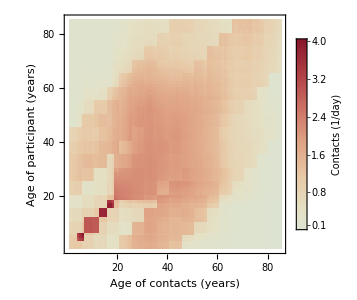
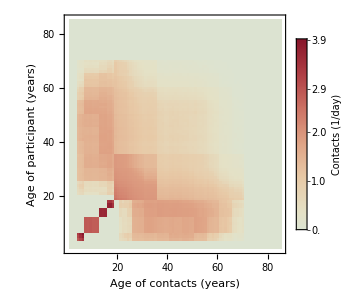
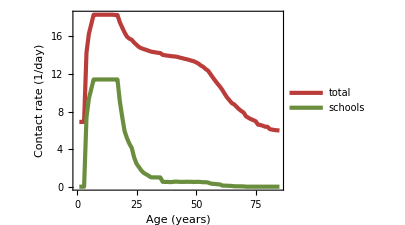
-Graphics- |  | -Graphics-
 | -Graphics- |

```mathematica
(* Importing Data *)
schoolContactsMultiplier = 11.41;
demographyData85=Import["../data/Portugal_country_level_age_distribution_85.csv"]⟦All,2⟧;
contactDataBefore85=Import["../data/Portugal_country_level_M_overall_contact_matrix_85.csv"];
schoolRawContactDataBefore85=  Import["../data/Portugal_country_level_F_school_setting_85.csv"];
schoolContactDataBefore85 = schoolContactsMultiplier * schoolRawContactDataBefore85;


(* Get the total contacts per participant *)calculateContactsAgeGroups2=Table[Total[contactDataBefore85⟦k,All⟧],{k,85}];
calculateSchoolContactsAgeGroups2=Table[Total[schoolContactDataBefore85⟦k,All⟧],{k,85}];


(* Plotting *)figTotalContPerAge = LINEPLOT[{calculateContactsAgeGroups2, calculateSchoolContactsAgeGroups2},{colorDarkRainbow[[11]], colorDarkRainbow[[5]]},"","Age (years)","Contact rate (1/day)",{"total", "schools"}, {}];
figTotalConmat = CONTACTMATRIXPLOT[contactDataBefore85, "ThermometerColors" ,""];
figSchoolConmat = CONTACTMATRIXPLOT[schoolContactDataBefore85, "ThermometerColors", ""];

figA = PLOTWITHLETTER[figTotalConmat, "a", "right"];
figB = PLOTWITHLETTER[figSchoolConmat, "b", "right"];
figC = PLOTWITHLETTER[figTotalContPerAge, "c", "right"];
figConts = Grid[{{figA,SpanFromLeft, figB}, {SpanFromLeft, figC, SpanFromLeft}}];
If[showFigs, figConts]
```

### TRANSFORMING THE CONTACT MATRICES FROM 86x86 TO 10x10

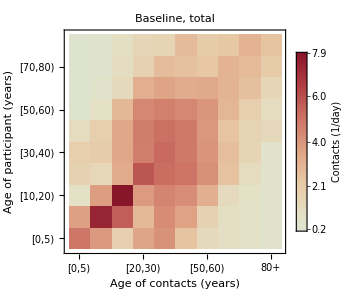
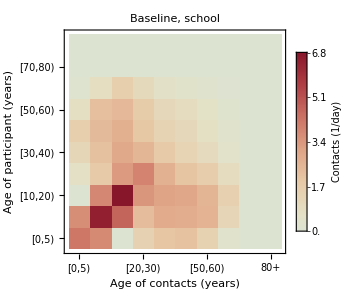
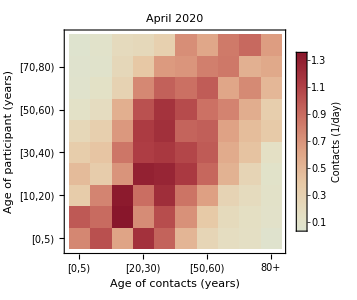
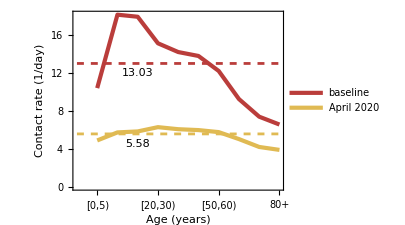
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(* Demographic data for 86+
https://www.pordata.pt/Portugal/Popula%C3%A7%C3%A3o+residente++m%C3%A9dia+anual+total+e+por+grupo+et%C3%A1rio-10 *)
demog86Plus = 316442;


(* Getting the ratio of lockdown contacts based on NL data *)
contactDataNLBefore10=Import["../data/CONTACT MATRIX NL BEFORE 10.csv"];
contactDataNLAfter10=Import["../data/CONTACT MATRIX NL AFTER 10.csv"];
contactRatioNL10=contactDataNLAfter10/contactDataNLBefore10;


(* Function transforming the 1x86 age groups to 1x10 *)
transformList86to10[list85_]:=Total/@Join[Partition[list85,5]⟦1;;2⟧,Partition[list85,10]⟦2;;⟧,{list85⟦81;;⟧}];
demographyData86=Append[demographyData85, demog86Plus];
demographyData10=transformList86to10[demographyData86];


(* Creating the 86x86 contact matrices *)
transformMatrix85to86[mat85_]:=Join[Join[mat85,{mat85⟦85⟧}],List/@(Join[mat85,{mat85⟦85⟧}]⟦All,85⟧ demographyData86⟦86⟧/demographyData86⟦85⟧), 2];
contactDataBefore86=transformMatrix85to86[contactDataBefore85];
schoolContactDataBefore86=transformMatrix85to86[schoolContactDataBefore85];


(* Creating the 10x10 contact matrices*)
contactDataBefore10=transformList86to10[ Transpose[transformList86to10[Transpose[contactDataBefore86]]] demographyData86]/demographyData10;
contactDataAfter10=contactDataBefore10 * contactRatioNL10 ;
schoolContactDataBefore10=transformList86to10[ Transpose[transformList86to10[Transpose[schoolContactDataBefore86]]] demographyData86]/demographyData10;

(* Exporting data *)
If[exportData,
Export["../data/DEMOGRAPHY PT 86 V.csv",demographyData86,"Table"];Export["../data/DEMOGRAPHY PT 10 V.csv",demographyData10,"Table"];
Export["../data/CONTACT MATRIX PT BEFORE 10 V.csv",contactDataBefore10,"Table"];
Export["../data/CONTACT MATRIX PT AFTER 10 V.csv",contactDataAfter10,"Table"];
Export["../data/SCHOOL CONTACT MATRIX PT BEFORE 86 V.csv",schoolContactDataBefore86,"Table"];
Export["../data/SCHOOL CONTACT MATRIX PT BEFORE 10 V.csv",schoolContactDataBefore10,"Table"]];


(* Get the total contacts per participant *)calculateContactsAgeGroupsBefore=Table[Total[contactDataBefore10⟦k,All⟧],{k,ageGroups}];
calculateContactsAgeGroupsAfter=Table[Total[contactDataAfter10⟦k,All⟧],{k,ageGroups}];

calculateAverageContactRateBefore=Sum[calculateContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,ageGroups}];
calculateAverageContactRateAfter=Sum[calculateContactsAgeGroupsAfter⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,ageGroups}];

(* Plotting *)
figContactMatrixBefore = CONTACTMATRIXPLOT[contactDataBefore10, "ThermometerColors" ,"Baseline, total", "contacts 10"];
figSchoolContactMatrixBefore = CONTACTMATRIXPLOT[schoolContactDataBefore10, "ThermometerColors" ,"Baseline, school","contacts 10"];
figContactMatrixAfter = CONTACTMATRIXPLOT[contactDataAfter10, "ThermometerColors", "April 2020", "contacts 10"];
figTotalContPerAge =
Show[LINEPLOT[{calculateContactsAgeGroupsBefore, calculateContactsAgeGroupsAfter},{colorDarkRainbow[[11]], colorDarkRainbow[[8]]},"","Age (years)","Contact rate (1/day)",{"baseline", "April 2020"},
 "contacts 10"],
 Plot[calculateAverageContactRateBefore,{x,0,11}, PlotStyle->{colorDarkRainbow[[11]], Dashed}],
Plot[calculateAverageContactRateAfter,{x,0,11}, PlotStyle->{colorDarkRainbow[[8]], Dashed}],
Graphics[{Style[Text[ToString[Round[calculateAverageContactRateBefore,0.01]], {3, calculateAverageContactRateBefore-0.5}, {0.1, 0.9}], FontSize->sizeFontSmall]}],
Graphics[{Style[Text[ToString[Round[calculateAverageContactRateAfter,0.01]], {3, calculateAverageContactRateAfter-0.5}, {0.1, 0.9}], FontSize->sizeFontSmall]}]];

figA = PLOTWITHLETTER[figContactMatrixBefore, "a", "right"];
figB = PLOTWITHLETTER[figSchoolContactMatrixBefore, "b", "right"];
figC = PLOTWITHLETTER[figContactMatrixAfter, "c", "right"];
figD = PLOTWITHLETTER[figTotalContPerAge, "d", "right"];
figConts = Grid[{{figA, figB}, {figC, figD}}];
If[showFigs, figConts]

figNames={"SFig1A","SFig1B","SFig1C"};
figArray={figA,figB,figC, figD};
(*If[exportFigs,Table[Export[StringJoin["../figures/",figNames⟦j⟧,exportFormat⟦i⟧],figArray⟦j⟧],{i,1,Length[exportFormat]},{j,1,Length[figNames]}]];*)
```

## Hospitalization data